```mathematica
datas = Table[Flatten[Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\output_"<>ToString[i]<>".csv"]],{i,0,19}];
```

```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data";(*Replace with your folder path*)files=FileNames["*.csv",folder];
tables=Import[#]&/@files;
```

```mathematica
data = Table[Flatten[t],{t,tables}];
```

```mathematica
sortedData=Sort[data,Mean[#1]>Mean[#2]&];
```

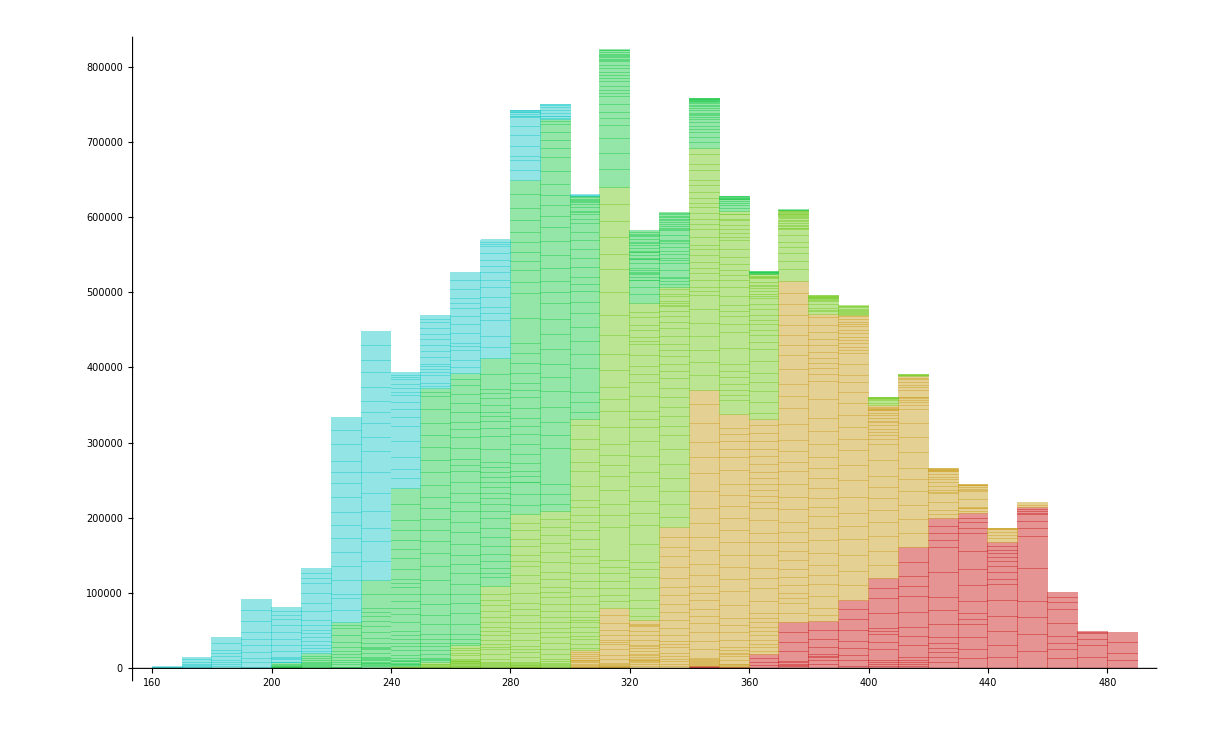

$Aborted[]

```mathematica
generateColors[n_]:=Table[Hue[Round[i/(2*n),.25/2],.8,.8],{i,n}];

Histogram[sortedData,ChartStyle->generateColors[Length[sortedData]],ChartLayout->"Stacked",ChartBaseStyle->EdgeForm[None]]
```